```mathematica
robberArrest[robberCo_, police1cord_, police2cord_, speed_, timestep_, stepnumb_]:=
Module[
{police1co = police1cord,
police2co = police2cord, 
police1Slope,
police2Slope, 
police1Done=False, 
police2Done=False,
dY, 
dX,
dX2, 
dY2, 
filler,
police1Points = {},
startingPoints,
display,
police2Points = {}, 
L = speed*timestep, 
i},  
(*Get police 1 slope info*)
If[police1co[[1]]==robberCo[[1]], police1Slope="undef",
police1Slope = (police1co[[2]]- robberCo[[2]])/(police1co[[1]] - robberCo[[1]])];
If[police2co[[1]]==robberCo[[1]], police2Slope="undef",
police2Slope = (police2co[[2]]- robberCo[[2]])/(police2co[[1]] - robberCo[[1]])];
If[
police1Slope≠ 0&&police1Slope≠ "undef",
dY = √(L^2/((1/police1Slope^2) + 1));
dX= √(L^2/(1 + police1Slope^2))];
If[police1Slope==0, 
dY = 0;
dX = √(L^2/(1 + police1Slope^2));
];
If[police1Slope=="undef", 
dY=1;
dX=0];

(*Get police 2 slope info*)
If[
police2Slope≠ 0&&police2Slope≠"undef",
dY2 = √(L^2/((1/police2Slope^2) + 1));
dX2=  √(L^2/(1 + police2Slope^2))];
If[police2Slope==0,
dY2 = 0;
dX2 = √(L^2/(1 + police2Slope^2));
];
If[police2Slope=="undef", 
dY2=1;
dX2=0];

For[
i = 1, 
i ≤ stepnumb, 
i++, 
(*Police 1 points *)
If[!police1Done, 
If[
police1Slope==  "undef"&& police1co[[2]] >robberCo[[2]], AppendTo[police1Points, {police1co[[1]]- dX, police1co[[2]]-dY}];
police1co = {police1co[[1]]- dX, police1co[[2]]-dY},
i
];
If[
police1Slope==  "undef"&& police1co[[2]] <robberCo[[2]], AppendTo[police1Points, {police1co[[1]]+dX, police1co[[2]]+dY}];
police1co = {police1co[[1]]+ dX, police1co[[2]]+dY},
i
];
If[
police1Slope==  0 && police1co[[1]] >robberCo[[1]], AppendTo[police1Points, {police1co[[1]]- dX, police1co[[2]]-dY}];
police1co = {police1co[[1]]- dX, police1co[[2]]-dY},
i
];
If[
police1Slope==  0 && police1co[[1]] <robberCo[[1]], AppendTo[police1Points, {police1co[[1]]+ dX, police1co[[2]]+dY}];
police1co = {police1co[[1]]+ dX, police1co[[2]]+dY},
i
];
If[
police1Slope < 0 && police1co[[1]] <robberCo[[1]], AppendTo[police1Points, {police1co[[1]]+ dX, police1co[[2]] - dY}];
police1co = {police1co[[1]]+ dX, police1co[[2]] - dY},
i
];
If[
police1Slope < 0 && police1co[[1]] >robberCo[[1]], AppendTo[police1Points, {police1co[[1]]- dX, police1co[[2]] + dY}];
police1co = {police1co[[1]]- dX, police1co[[2]] + dY},
i
];
If[
police1Slope> 0 && police1co[[1]] <robberCo[[1]], AppendTo[police1Points, {police1co[[1]]+ dX, police1co[[2]] + dY}];
police1co = {police1co[[1]]+ dX, police1co[[2]] + dY},
i
];
If[
police1Slope> 0 && police1co[[1]] >robberCo[[1]], AppendTo[police1Points, {police1co[[1]]- dX, police1co[[2]] - dY}];
police1co = {police1co[[1]]- dX, police1co[[2]] - dY},
i
],
(*else*)
police1Points={{robberCo[[1]], robberCo[[2]]}}
];

(*Police 2 points *)
If[!police2Done,
If[
police2Slope==  "undef" && police2co[[2]] >robberCo[[2]], AppendTo[police2Points, {police2co[[1]]- dX2, police2co[[2]]-dY2}];
police2co = {police2co[[1]]- dX2, police2co[[2]]-dY2},
i
];
If[
police2Slope=="undef" && police2co[[1]] <robberCo[[1]], AppendTo[police2Points, {police2co[[1]]+ dX2, police2co[[2]]+dY2}];
police2co = {police2co[[1]]+ dX2, police2co[[2]]+dY2},
i
];
If[
police2Slope==  0 && police2co[[1]] >robberCo[[1]], AppendTo[police2Points, {police2co[[1]]- dX2, police2co[[2]]-dY2}];
police2co = {police2co[[1]]- dX2, police2co[[2]]-dY2},
i
];
If[
police2Slope==  0 && police2co[[1]] <robberCo[[1]], AppendTo[police2Points, {police2co[[1]]+ dX2, police2co[[2]]+dY2}];
police2co = {police2co[[1]]+ dX2, police2co[[2]]+dY2},
i
];
If[
police2Slope < 0 && police2co[[1]] <robberCo[[1]], AppendTo[police2Points, {police2co[[1]]+ dX2, police2co[[2]] - dY2}];
police2co = {police2co[[1]]+ dX2, police2co[[2]] - dY2},
i
];
If[
police2Slope < 0 && police2co[[1]] >robberCo[[1]], AppendTo[police2Points, {police2co[[1]]- dX2, police2co[[2]] + dY2}];
police2co = {police2co[[1]]- dX2, police2co[[2]] + dY2},
i
];
If[
police2Slope> 0 && police2co[[1]] <robberCo[[1]], AppendTo[police2Points, {police2co[[1]]+ dX2, police2co[[2]] + dY2}];
police2co = {police2co[[1]]+ dX2, police2co[[2]] + dY2},
i
];
If[
police2Slope> 0 && police2co[[1]] >robberCo[[1]], AppendTo[police2Points, {police2co[[1]]- dX2, police2co[[2]] - dY2}];
police2co = {police2co[[1]]- dX2, police2co[[2]] - dY2},
i]
,
(*else*)
police2Points={{robberCo[[1]], robberCo[[2]]}}
]
];
police1Points=DeleteCases[police1Points, {}];
police2Points=DeleteCases[police2Points, {}];
display =ListPlot[{police1Points, police2Points}, Joined -> True, Axes->False];
Print[police2Points];
(*Plot everything*)
startingPoints = ListPlot[{{robberCo},{police1cord},{police2cord}},PlotStyle -> {{Red,PointSize[Large]}, {Black,PointSize[Large]},{Black,PointSize[Large]}}]; 
 Show[startingPoints, display, Axes -> False]
]
```

ListPlot::lpn: {{{7, 0}}, {}} is not a list of numbers or pairs of numbers.

{}

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[1, 0, 0], PointSize[Large]], PointBox[List[List[7.`, 0.`]]], Hue[0.9060679774997897`, 0.6`, 0.6`], Directive[GrayLevel[0], PointSize[Large]], PointBox[List[List[2.`, 1.1`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[2.`, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[2.`, 7.`], List[0, 1.1`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.1`, 0.1`], List[0.022000000000000002`, 0.022000000000000002`]]]]], ListPlot[{{{7, 0}}, {}}, Joined → True, Axes → False], Axes → False.

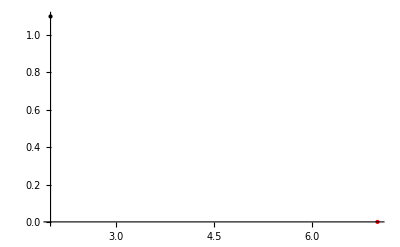
Show[-Graphics-,ListPlot[{{{7,0}},{}},Joined→True,Axes→False],Axes→False]

```mathematica
robberArrest[{7,0},{7,0},{2,1.1},1,.01,250]
```

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[1, 0, 0], PointSize[Large]], PointBox[List[List[0.`, 0.`]]], Hue[0.9060679774997897`, 0.6`, 0.6`], Directive[GrayLevel[0], PointSize[Large]], PointBox[List[List[0.`, 5.`]]], Hue[0.1421359549995791`, 0.6`, 0.6`], Directive[GrayLevel[0], PointSize[Large]], PointBox[List[List[5.`, 0.`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0, 5.`], List[0, 5.`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.1`, 0.1`], List[0.1`, 0.1`]]]]], ListPlot[{{}, {}}, Joined → True, Axes → False], Axes → False.

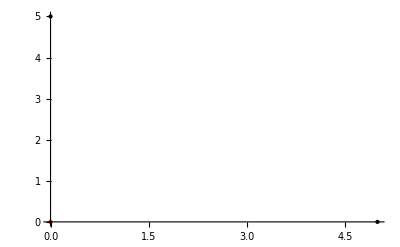
Show[-Graphics-,ListPlot[{{},{}},Joined→True,Axes→False],Axes→False]

```mathematica
robberArrest[{0,0},{0,5},{5,0},1,.01,110]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[1, 0, 0], PointSize[Large]], PointBox[List[List[-1.`, -1.`]]], Hue[0.9060679774997897`, 0.6`, 0.6`], Directive[GrayLevel[0], PointSize[Large]], PointBox[List[List[2.`, 1.1`]]], Hue[0.1421359549995791`, 0.6`, 0.6`], Directive[GrayLevel[0], PointSize[Large]], PointBox[List[List[0.`, 0.`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0.`, 0.`]], Rule[Method, List[]], Rule[PlotRange, List[List[-1.`, 2.`], List[-1.`, 1.1`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.06`, 0.06`], List[0.042`, 0.042`]]]]], ListPlot[{{}, {}}, Joined → True, Axes → False], Axes → False.

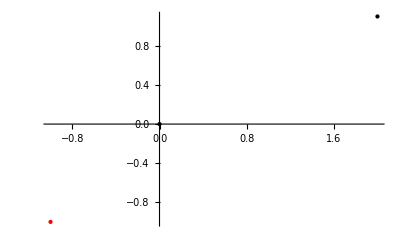
Show[-Graphics-,ListPlot[{{},{}},Joined→True,Axes→False],Axes→False]

```mathematica
robberArrest[{-1,-1},{2,1.1},{0,0},1,.01,110]
```

```mathematica
robberArrest[{0,0},{0,5}, {5,0}, 1, .01, 9900]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[1, 0, 0], PointSize[Large]], PointBox[List[List[0.`, 0.`]]], Hue[0.9060679774997897`, 0.6`, 0.6`], Directive[GrayLevel[0], PointSize[Large]], PointBox[List[List[0.`, 5.`]]], Hue[0.1421359549995791`, 0.6`, 0.6`], Directive[GrayLevel[0], PointSize[Large]], PointBox[List[List[5.`, 0.`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0, 5.`], List[0, 5.`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.1`, 0.1`], List[0.1`, 0.1`]]]]], ListPlot[{{}, {}}, Joined → True, Axes → False], Axes → False.

Show[-Graphics-,ListPlot[{{},{}},Joined→True,Axes→False],Axes→False]